# Force-free Current Sheet

```mathematica
PacletDirectoryLoad["~/src/Beforerr.m"];
<<Beforerr`;
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
(* Change the directory to the current file location *)
SetDirectory@NotebookDirectory[];

SaveP[suffix_:""]:=Module[{},
ExportP["profiles"<>suffix,p1];
ExportP["J_profiles"<>suffix,p2];
ExportP["s1_profiles"<>suffix,pn1];
]
```

## MHD

```mathematica
Vx[z_]:=V0 Cos[φ[z]]
Vy[z_]:=V0 Sin[φ[z]]
Bx[z]:=B0 Cos[φ[z]]
By[z]:=B0 Sin[φ[z]]

V:={Vx[z],Vy[z],Vz[z]};
B:={Bx[z],By[z],Bz};
r={x,y,z};
J:=Curl[B,r]
(*J:={Jx,Jy,Jz}*)
eqM:=Γ  D[V,z]+Grad[p[z],r]==J×B
eqM
```

{-V0 Γ Sin[φ[z]] φ'[z],V0 Γ Cos[φ[z]] φ'[z],p'[z]+Γ Vz'[z]}=={-B0 Bz Sin[φ[z]] φ'[z],B0 Bz Cos[φ[z]] φ'[z],0}

```mathematica
eqM1:=-V0 Γ Sin[φ[z]] φ'[z]==-B0 Bz Sin[φ[z]] φ'[z]//Simplify
eqM2:=V0 Γ Cos[φ[z]] φ'[z]==B0 Bz Cos[φ[z]] φ'[z]//Simplify
{eqM1,eqM2}
```

{(B0 Bz-V0 Γ) Sin[φ[z]] φ'[z]==0,(B0 Bz-V0 Γ) Cos[φ[z]] φ'[z]==0}

## Multiple - Fluid

```mathematica
multiFluidConds={
Jx->Jxi+Jxe,Jy->Jyi+Jye,
Jxe->-(Γe Bx)/Bz,Jye->-(Γe By)/Bz,
Jxi->Λx n1 u1x,Jyi->Λy n1 u1y,
ux->(Λx n1 u1x)/n,uy->(Λy n1  u1y)/n
};
forceFreeConds={
Bx->B0 Cos[φ[z]],
By->B0 Sin [φ[z]],
u1x->u1 Cos [φ[z]],
u1y->u1 Sin[φ[z]]
};
twoFluidConds={
n->n2+n1
};

conds=Join[multiFluidConds,forceFreeConds,twoFluidConds];

assums={B0≠0};
notationRules={
B0->Subscript[B, 0],Bx->Subscript[B, x],By->Subscript[B, y],Bz->Subscript[B, z],
ux->Subscript[U, x],uy->Subscript[U, y],u1->Subscript[u, 1],
Jx->Subscript[J, x],Jy->Subscript[J, y],Jxi->Subscript[J, x,i],Jyi->Subscript[J, y,i],
Γ1->Subscript[Γ, 1],n1->Subscript[n, 1],Λz->Subscript[Λ, z],Λy->Subscript[Λ, y]
};
```

```mathematica
eqφ:={φ'[z]==Bz/Γ1(n1Inf-n1),φ[0]==π/2};
eqT:={Γ1^2/n1+1/2(n1 T1[z])==Γ1^2+1/2 T0};
eqs=Join[eqφ,eqT];

s={n1->1+c1/(1+(z/δ )^2)};

rulesn={Bz->1,δ->1,u1->(Γ1 B0)/(n1Inf Bz),u2->-(Γ2 B0)/(n2Inf Bz),n1Inf->1,Γ1->-1/(√(1+λnInf λzInf^2)),n2Inf->λnInf n1Inf};
sol1=DSolve[eqs/.s,{φ[z],T1[z]},z]//First;

eqUB:=((-Λy u1)/B0+Bz/Γ1)n1+(Λz Γ1)/Bz==B0/u1
sol2=Solve[eqUB/.s,Λy ]//First;

sols=Join[s,sol1,sol2];
```

```mathematica
ΛyTemp=Λy/.sol2;
Simplify[ΛyTemp//.rulesn]
{n1,Bx,By,u1x,u1y}/.sols//.rulesn
(*Asymptotic[ΛyTemp//.rulesn/.{Λz->-1,z->0}]*)
```

(c1+Λz+z^2 Λz+c1 λnInf λzInf^2)/(1+c1+z^2)

{1+c1/(1+z^2),Bx,By,u1x,u1y}

```mathematica
Γ2:=(Λz-1) Γ1
Λz:=λzInf λnInf +1
Γe:=Λz Γ1
Λx:=Λy
```

Normalize the thickness by δ (let δ=1) and

```mathematica
n2:=Γ2/Γ1 n1-(B0/u1+B0/u2)Γ2/Bz
u2x:=((Λx-1) n1 u1x)/n2
u2y:=((Λy-1) n1 u1y)/n2
uu:=Simplify[√(ux^2+uy^2)]
```

```mathematica
profile={Bx,By,n,ux,uy}
```

{Bx,By,n,ux,uy}

```mathematica
Manipulate[
tempRules={B0->B0i,c1->ci,λnInf->λnInfi,λzInf->λzInfi,T0->T0i};
profilePlot[profile_]:=Plot[
Evaluate[profile//.conds/. sols//.rulesn/.tempRules],{z,-zmaxi,zmaxi},
PlotLegends->Evaluate[profile/.notationRules],AxesLabel->{"z",Automatic}
];

p1profile=profile;
p1=profilePlot[profile];
p2=profilePlot[{Λy-1,Jx,Jy,Jxi,Jyi}];

(*pn1=Plot[
Evaluate[{n1,u1x,u1y,T1[z],n1 T1[z]}/.sols//.rulesn],
{z,-zmax,zmax},PlotLegends->{HoldForm[Subscript[n, 1]],Subscript[u, 1,x],Subscript[u, 1,y],Subscript[T, 1],Subscript[p, 1]}
];
pn2=Plot[
Evaluate[{n2,u2x,u2y,T2[z],n2 T2[z],Subscript[p, 2]}/.sols//.rulesn],
{z,-zmax,zmax},PlotLegends->{HoldForm[Subscript[n, 2]],Subscript[u, 2,x],Subscript[u, 2,y],Subscript[T, 2],Subscript[p, 1]}
];*)

(*p3=Plot[Evaluate[{ux,uy,Bx/√n,By/√n}/.sols//.rulesn],{z,-zmax,zmax}];*)

(*If[λnInfi<0.01,
SaveP[suffix="_one"]
];*)
{p1,p2}
,
{{λnInfi,1} ,0,2},
{{λzInfi,-1} ,-2,0},
{{ci,1/Sqrt[2]},0,2},
{{B0i,2},0.5,2},
{T0i,1,2},
{{zmaxi,10},5,30}
]
```

```mathematica
conf={ratio->0.5};
```

```mathematica
Bys=By/.conds/.sols//.rulesn;
cond=(Bys/.z->∞)==ratio(Bys/.z->0)/.conf;
cond=Simplify[cond,assums]
condRule2=Solve[cond,c1]
(*Solve[cond]*)
```

1. Cos[1/2 c1 π √(1+λnInf λzInf^2)]==0.5

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c1→-(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)},{c1→(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)}}

```mathematica
ratioList=Range[0.001,0.501,0.1];
ratio2λn[r_]:=(1-r)/r
(*λnInfList={1,2,5,10};*)
λnInfList=ratio2λn/@ratioList;

λnLegend[λ_]:="λ_n="<>ToString[Round[λ]]
ratioLegend[r_]:="n_1="<>ToString[Round[r,0.1]]
```

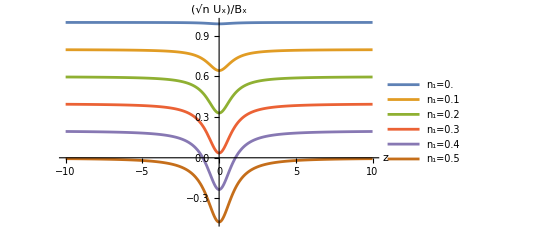
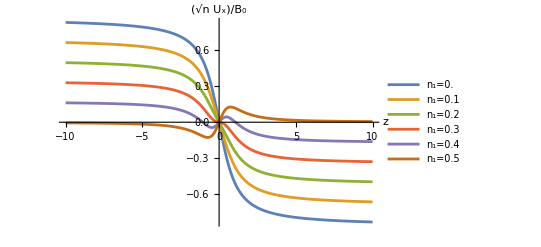
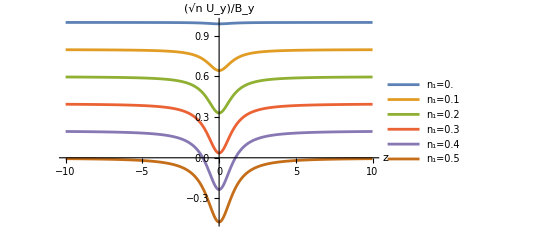
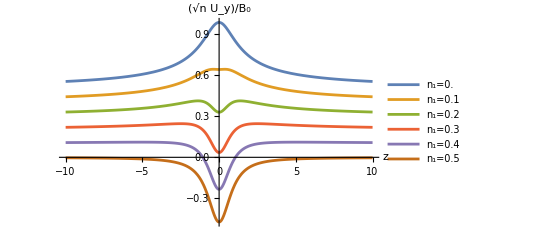

```mathematica
exps={ux/(Bx/√n), ux/(B0/√n),uy/(By/√n),uy/(B0/√n)};
ps=Block[{B0i=2,λzInf=-1,zmax=10},
tempRules={λnInf->λnInfList,B0->B0i};
legends=ratioLegend/@ratioList;
tempPlot[v_]:=Plot[
Evaluate[v//. conds/.sols//.rulesn/.Last@ condRule2/.tempRules],{z,-zmax,zmax},
PlotLegends->legends,AxesLabel->{"z",v/.notationRules}
];
tempPlot/@exps
]
(*ExportP["UxNorm",ps[[2]]];
ExportP["UyNorm",ps[[4]]];*)
```

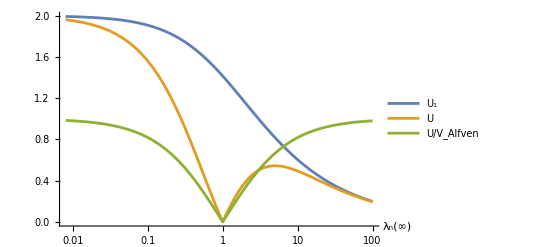

```mathematica
Block[{B0=2,λzInf=-1,zmax=10,tempExps},
tempRules= z->1000;
exp={Abs@u1,uu,uu/(B0/√n)};
tempExps=Simplify[exp//.conds/.sols//.rulesn/.Last@ condRule2/.tempRules];
p=LogLinearPlot[tempExps,{λnInf,0.008,100},PlotLegends->{Subscript[U, 1],U,"U/V_Alfven"},AxesLabel->{"λ_n(∞)",None}];
(*saveP["vRatios",p];*)
p
]
```

```mathematica
(*Define the system of equations*)
eq1:=D[Bx[z],z]==n1[z] u1y[z]+n2 u2y-GammaE By[z]/Bz;
eq2:=D[By[z],z]==-n1[z] u1x[z]-n2 u2x+GammaE Bx[z]/Bz;
eq3:=Gamma1 D[u1x[z],z]==n1[z] u1y[z] Bz-Gamma1 By[z];
eq4:=Gamma1 D[u1y[z],z]==Gamma1 Bx[z]-n1[z] u1x[z] Bz;
eq5:=D[(Gamma1^2/n1[z]+C1 n1[z]^γ/2),z]==n1[z] (u1x[z] By[z]-u1y[z] Bx[z]-Te/(2 ne) D[ne,z]);
ne:=n2+ n1[z];


u1xInf:=Gamma1 BxInf/(n1Inf Bz)
u1yInf:=Gamma1 ByInf/(n1Inf Bz)
bc1=Bx[zmin]==0;
bc2:=n1[zmax]==n1Inf+eps;
bc3:=Bx[zmax]==1-eps;
bc4:=By[zmax]==ByInf+eps;
bc6:=u1y[zmax]==u1yInf+eps;
bc5:=u1x[zmax]==u1xInf+eps;

BxInf=1;
γ=5/3;
zmax=10;
eps=0.01;
```

Plot::nonopt: Options expected (instead of PlotLegends→{B0 Cos[φ[z]],B0 Sin[φ[z]],n1+n1 λnInf λzInf-((B0 Power[«2»]+B0 Power[«2»]) Γ1 λnInf λzInf)/Bz,(n1 u1 Λy Cos[φ[z]])/(n1+n1 λnInf λzInf-Power[«2»] Plus[«2»] Γ1 λnInf λzInf),(n1 u1 Λy Sin[φ[z]])/(n1+n1 λnInf λzInf-Power[«2»] Plus[«2»] Γ1 λnInf λzInf)}/.notationRules) beyond position 2 in Plot[{2 Cos[0.50025 (-3.14002-Power[«2»] ArcTan[«1»])],«3»,(1.001 (3.40851+«18» z^2) (1+«1») Sin[0.50025 (-3.14002-Power[«2»] ArcTan[«1»])])/((1+1/(√2)+z^2) (1.002+1/(√2 Plus[«2»])-0.001 (1+Times[«2»])))},{z,-zmax,zmax},PlotLegends→{«1»}/.notationRules,AxesLabel→{z}]. An option must be a rule or a list of rules.

## Another normalization

```mathematica
num=2;
eqAmJy:=Hold[D[Bx,z]]==Sum[Subscript[n, α] Subscript[uy, α],{α,num}]-ne uey
eqM1u[α_]:=Subscript[Γ, α] Hold@D[Subscript[ux, α],z]==Subscript[n, α] Subscript[uy, α] Bz - Subscript[Γ, α] By
forceFreeConds={
Bx->B0 Cos[θ[z]],
By->B0 Sin [θ[z]],
Subscript[uy, α_]:>Subscript[u, α] Sin[θ[z]],
Subscript[ux, α_]:>Subscript[u, α] Cos[θ[z]],
uey->(Γe By)/(ne Bz)
};
normRules={
Γe->Sum[Subscript[Γ, α],{α,num}],
Subscript[n, α_]:>Subscript[λ, α,n] Subscript[nInf, α],Subscript[nInf, α_]:>Subscript[C, α,n] Subscript[n, e,Inf],Subscript[u, α_]:>Subscript[C, α,u] Bz/(√Subscript[n, e,Inf]),
Subscript[Γ, α_]:>Subscript[nInf, α] Subscript[uzInf, α],Subscript[uzInf, α_]:>Subscript[C, α,uz] Bz/(√Subscript[n, e,Inf])
};
nRules={Subscript[n, e,Inf]->1,Bz->1};
Simplify[ReleaseHold[{eqAmJy,eqM1u[1]}//.forceFreeConds//.normRules/.nRules],Subscript[C, 1,n] !=0]
```

{Sin[θ[z]] (C_(1,n) (B0 C_(1,uz)-C_(1,u) λ_(1,n))+C_(2,n) (B0 C_(2,uz)-C_(2,u) λ_(2,n))-B0 θ'[z])==0,Sin[θ[z]] (C_(1,u) λ_(1,n)+C_(1,uz) (-B0+C_(1,u) θ'[z]))==0}

```mathematica
asymEq:=Bz^2==Sum[Subscript[Γ, α]^2/Subscript[nInf, α],{α,num}]
nEq:=1==Sum[Subscript[C, α,n],{α,num}]
(asymEq&&nEq)//.normRules/.nRules
```

1==C_(1,n) C_(1,uz)^2+C_(2,n) C_(2,uz)^2&&1==C_(1,n)+C_(2,n)

```mathematica
eqTwoθ:=(Subscript[C, 1,n] Subscript[C, 1,u] Subscript[λ, 1,n]+Subscript[C, 2,n] Subscript[C, 2,u] Subscript[λ, 2,n]-B0 Γe)/B0==(Subscript[C, 1,u] Subscript[λ, 1,n]-Subscript[C, 1,uz] B0)/(Subscript[C, 1,u] Subscript[C, 1,uz])
λ2sol=First@Solve[eqTwoθ//.normRules/.nRules,Subscript[λ, 2,n]]
```

{λ_(2,n)→(-B0^2 C_(1,uz)+B0 C_(1,n) C_(1,u) C_(1,uz)^2+B0 C_(1,u) C_(1,uz) C_(2,n) C_(2,uz)+B0 C_(1,u) λ_(1,n)-C_(1,n) C_(1,u)^2 C_(1,uz) λ_(1,n))/(C_(1,u) C_(1,uz) C_(2,n) C_(2,u))}

```mathematica
asymConds={
Subscript[C, 1,u]->Subscript[C, 1,uz] B0,
Subscript[C, 2,u]->Subscript[C, 2,uz] B0
};
eqθ:={Subscript[C, 1,u] Subscript[λ, 1,n]+Subscript[C, 1,uz] (-B0+Subscript[C, 1,u] θ'[z])==0,θ[0]==π/2}
s={Subscript[λ, 1,n]->1+c/(1+z^2)};
sol=First@DSolve[eqθ/.asymConds/.s,θ[z],z]
```

{θ[z]→(-2 c ArcTan[z]+π C_(1,uz))/(2 C_(1,uz))}

```mathematica
eqRules={
nTotal->Sum[Subscript[n, α] ,{α,num}]
};
rules=Join[forceFreeConds,normRules,nRules,asymConds,sol,λ2sol,eqRules];
```

```mathematica
{Bx,nTotal}//.rules//.temprule/.s
```

{B0 Cos[1/2 (π-2 c ArcTan[z])],0.6 (1+c/(1+z^2))-(-0.8 B0^2+0.4 B0^2 (1+c/(1+z^2)))/B0^2}

{Bx,By,nTotal,ux,uy}

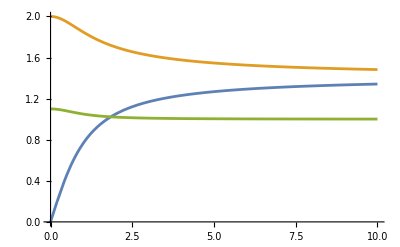

```mathematica
profile={Bx,By,nTotal,ux,uy}
Block[{B0=2,c=0.5,c1=0.6},
temprule={Subscript[C, 1,n]->c1,Subscript[C, 2,n]->1-Subscript[C, 1,n],Subscript[C, 1,uz]->1,Subscript[C, 2,uz]->-1};
Plot[Evaluate[profile//.rules//.temprule/.s],{z,0,10},PlotRange->All]
]
```